```mathematica
Clear["Global`*"];
(* All in mkm *)
```

```mathematica
λ=1.55;
β=(2π)/λ;
CalcWindow=1000;
N0=511;
ω0=100;
```

```mathematica
q0=N[(π ω0^2)/(I λ)];
zR=Re[I q0]
```

20268.3

```mathematica
ω[z_]:=N[ω0 √(1+((λ z)/(π ω0^2))^2)];
R[z_]:=N[z(1+((π ω0^2)/(λ z))^2)];
q[z_]:=Piecewise[{{(-1/R[z]+I λ/(π ω[z]^2))^-1,z<0||z>0}},q0];
Gauss[r_,z_]:=N[Exp[I(β r^2)/2 1/q[z]]];
StepR[r_]:=Piecewise[{{1.,0≤r^2<ω0^2},{0,r^2≥ω0^2}}];
```

```mathematica
Lence[r_,f_]:=N[Exp[(I β r^2)/2-1/R[f]]];
LenceSpherical[r_,f_]:=N[Exp[(I β r^2)/(2 f)]];
LenseMatrix[f_]:=Array[Lence[√(#1^2+#2^2),f]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
StartBeam=Array[Gauss[√(#1^2+#2^2),0]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
D2Fourier=N[(π/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}]];
FourierOp[h_]:=Exp[I (D2Fourier h)/(2β)];
```

```mathematica
f=50000.;
LenceBeam=StartBeam×LenseMatrix[f];
Parallelize[FocusBeam=InverseFourier[FourierOp[f]× Fourier[LenceBeam ]];FourierFocus=RotateLeft[Fourier[StartBeam],{(N0+1)/2,(N0+1)/2}];]
```

{-Graphics-,-Graphics-,-Graphics-}

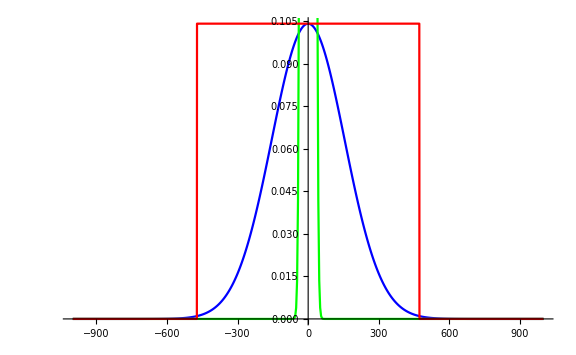
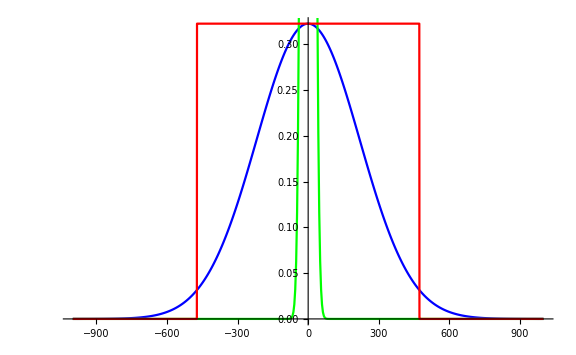

```mathematica
{ArrayPlot[Abs[StartBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],ArrayPlot[Abs[FocusBeam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium],ArrayPlot[Abs[FourierFocus]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]}
{Show[
ListPlot[Abs[FocusBeam[[(N0+1)/2]]]^2,
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Blue],ImageSize->Large],ListPlot[Abs[FourierFocus[[(N0+1)/2]]]^2(*×Max[Abs[FocusBeam[[(N0+1)/2]]]^2]/Max[Abs[FourierFocus[[(N0+1)/2]]]^2]*),
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Green],ImageSize->Large],Plot[Max[Abs[FocusBeam[[(N0+1)/2]]]^2]×UnitBox[r/(1.22 λ/ω0 f)],{r,-CalcWindow,CalcWindow},
ColorFunction->Function[{x,y},Red],Exclusions->None,ImageSize->Large]
],Show[
ListPlot[Abs[FocusBeam[[(N0+1)/2]]],
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Blue],ImageSize->Large],ListPlot[Abs[FourierFocus[[(N0+1)/2]]](*×Max[Abs[FocusBeam[[(N0+1)/2]]]]/Max[Abs[FourierFocus[[(N0+1)/2]]]]*),
Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Green],ImageSize->Large],Plot[Max[Abs[FocusBeam[[(N0+1)/2]]]]×UnitBox[r/(1.22 λ/ω0 f)],{r,-CalcWindow,CalcWindow},
ColorFunction->Function[{x,y},Red],Exclusions->None,ImageSize->Large]
]}
```

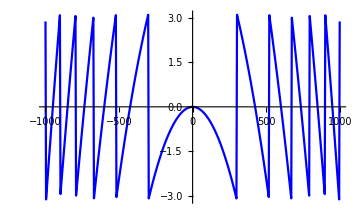
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[Arg[StartBeam],ImageSize->Medium],ArrayPlot[Arg[LenceBeam],ImageSize->Medium],
ListPlot[Arg[LenceBeam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All},ColorFunction->Function[{x,y},Blue],ImageSize->Medium]}
```

```mathematica
L=2f;
```

```mathematica
Beam=Parallelize[Table[Abs[InverseFourier[FourierOp[l] Fourier[LenceBeam ]][[(N0+1)/2]]]^2,{l,0,L,(L-0)/25}]];
```

```mathematica
ListPlot3D[Beam,PlotRange->All,ImageSize->Medium,DataRange->{{-CalcWindow,CalcWindow},{0,L}}]
```